```mathematica
BackScatterBoole=True;
```

```mathematica
Get["MergerTransport/Merger2D.m"]
```

Set::wrsym: Symbol pmax is Protected.

# Timing of manual integrand

```mathematica
RepeatedTiming[ManualphiAIntegrandAllLimitsShift[0,0,-0.02,{0,0.,900000.,Pi/4},{Pi,0.2,1,1,1,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],5]
```

{0.0024,0.000117158}

```mathematica
DeltaxDV2Shift[0.,0.,-0.02,900000.,Pi/4.,1.*Pi,0.2,1.,1.,0.,1.,1.,{0.,0.,0.}]
```

0.030017

```mathematica
DeltaxDV2ShiftCompiled[0.,0.,-0.02,900000.,Pi/4.,1.*Pi,0.2,1.,1.,0.,1.,1.,0.,0.,0.]
```

CompiledFunction::cfte: Compiled expression 0.030017 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

0.030017

```mathematica
Compiled
```

```mathematica
RepeatedTiming[bsFuncElectron2[900000.,Pi/4,1],5]
```

{0.00002,0.139082}

```mathematica
Plot3D[bsFuncElectron2[p,th0,1],{p,0,pmax},{th0,0,Pi/4}]
```

-Graphics3D-

```mathematica
RepeatedTiming[bsFuncElectron2Compiled[900000.,Pi/4,1],5]
```

{0.000013,0.139082}

```mathematica
ArcSin[-1000.]
```

-1.5708+7.6009 ⅈ

```mathematica
Compile
```

```mathematica
RepeatedTiming[ManualphiAIntegrandAllLimitsShift[0,0,-0.025,{0,0.,900000.,Pi/4},{Pi,0.2,1,1,1,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],5]
```

{0.0014,0.000422108}

## Not sure anymore if for values below, BS was on

### full transfer

```mathematica
{0.0023478055555555561`2.,0.000172985709316294}
```

### DY off

```mathematica
{0.0018567222222222223`2.,0.00017299659699305045}
```

### DxRx approx

```mathematica
{0.002799833333333333`2.,0.000172985243554352}
```

### full but beginning functions explicitly set

```mathematica
{0.00211053125`2.,0.000172985709316294}
```

### full but even more functions explicit

```mathematica
{0.0020393888888888883`2.,0.000172985709316294}
```

### DYRx and DxRx turned off

```mathematica
{0.0011851176470588235`2.,0.00017330651063544297}
```

### DxRx off

```mathematica
{0.0016426176470588235`2.,0.00017329564528380644}
```

# Timing of p limits

### DY on, DxRx off

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0054,{p,809743.,989698.,1.18728×10^6}}

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0056,{p,809743.,989698.,1.18728×10^6}}

### DY on, DxRx on

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0066,{p,810290.,990697.,1.18728×10^6}}

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0032,{p,0,1.18728×10^6}}

### both off

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.003,{p,809724.,989663.,1.18728×10^6}}

```mathematica
Table[RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2+0.2*x*10^-5,1,1,1,0.,1,1,0.03,0.01,{0.,0.,0.,0.}],3],{x,{0,8,16}}]
```

{{0.002,{p,809724.,989663.,1.18728×10^6}},{0.0025,{p,809789.,989742.,1.18728×10^6}},{0.0025,{p,809854.,989821.,1.18728×10^6}}}

```mathematica
ParallelTable[RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2+0.2*x*10^-5,1,1,1,0.,1,1,0.03,0.01,{0.,0.,0.,0.}],3],{x,{0,8,16}}]
```

{{0.0019,{p,809724.,989663.,1.18728×10^6}},{0.0019,{p,809789.,989742.,1.18728×10^6}},{0.002,{p,809854.,989821.,1.18728×10^6}}}

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0026,{p,809724.,989663.,1.18728×10^6}}

### DxRx on, DY off

```mathematica
RepeatedTiming[pXDomainShift[0,-0.02,Pi/4,Pi,0.2,1,1,1,0.,1,1,1,0.03,0.01,{0.,0.,0.,0.}],3]
```

{0.0094,{p,810271.,990662.,1.18728×10^6}}

# Function checks

```mathematica
xAShift[phiAlocal,yD,xD,plocal,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,{XAShift,YRxBShift,XDetShift,YDetShift}]
```

XAShift+(plocal rRxB Cos[phiAlocal] Sin[th0])/(299792458 BRxB rA)+√(1/rA) √rRxB (√(rD/rRxB) (xD-XDetShift-(plocal rRxB Cos[phiDet] Sin[th0])/(299792458 BRxB rD))+ArcTan[(alpha plocal (2-rRxB Sin[th0]^2))/(599584916 BRxB √(1-rRxB Sin[th0]^2) (R+YRxBShift+√(1/rRxB) √rRxB (-(alpha^2 plocal^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(plocal rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))) (1-G1 √(1/rRxB) √rRxB (-(alpha^2 plocal^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(plocal rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))+G2 (-(alpha^2 plocal^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(plocal rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))^2))] (R+YRxBShift+√(1/rRxB) √rRxB (-(alpha^2 plocal^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(plocal rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))))

```mathematica
DeltaxDV2Shift[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rD,phiDet,R,G1,G2,{YRxBShift,XDetShift,YDetShift}]
```

(p rRxB Cos[phiDV] Sin[th0])/(299792458 BRxB)+√rRxB (√(rD/rRxB) (xD-XDetShift-(p rRxB Cos[phiDet] Sin[th0])/(299792458 BRxB rD))+ArcTan[(alpha p (2-rRxB Sin[th0]^2))/(599584916 BRxB √(1-rRxB Sin[th0]^2) (R+YRxBShift+√(1/rRxB) √rRxB (-(alpha^2 p^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))) (1-G1 √(1/rRxB) √rRxB (-(alpha^2 p^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))+G2 (-(alpha^2 p^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))^2))] (R+YRxBShift+√(1/rRxB) √rRxB (-(alpha^2 p^2 (2-rRxB Sin[BRxB]^2)^2)/(179751035747363528 π^2 R th0^2 (1-rRxB Sin[BRxB]^2))+√(rD/rRxB) (yD-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)))))

```mathematica
pminApertShift[0.,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,0.03,0.01,{0.,0.,0.,0.}]
```

{630052.,1.64586×10^8,1.68312×10^8,1.05941×10^9}

```mathematica
pminApertCasesShift[0.,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,0.03,0.01,{0.,0.,0.,0.}]
```

630052.

```mathematica
RepeatedTiming[NSolve[0.03+0.01/2==xAShift[0.,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,{0.,0.,0.,0.}],plocal],5]
```

{0.0012,{{plocal→629785.}}}

```mathematica
RepeatedTiming[NSolve[0.03+0.01/2==xAShift[0.,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,{0.,0.,0.,0.}],plocal,Reals],5]
```

{0.0017,{{plocal→630052.},{plocal→1.64586×10^8},{plocal→1.68312×10^8},{plocal→1.05941×10^9}}}

```mathematica
RepeatedTiming[FindRoot[0.03+0.01/2==xAShift[0.,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,{0.,0.,0.,0.}],{plocal,pmax/2,0,2*pmax}],5]
```

{0.00076,{plocal→630052.}}

```mathematica
RepeatedTiming[FindRoot[0.03+0.01/2==xAShift[0.,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,{0.,0.,0.,0.}],{plocal,pmax/2,0,2*pmax},PrecisionGoal->5],5]
```

{0.000728,{plocal→630052.}}

```mathematica
RepeatedTiming[Solve[0.03+0.01/2==xAShift[0.,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,0.,1.,1.,1.,{0.,0.,0.,0.}],plocal,Reals],5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{0.079,{{plocal→630052.},{plocal→1.64586×10^8},{plocal→1.68312×10^8},{plocal→1.05941×10^9}}}

```mathematica
Solve[0.03+0.01/2==xAShift[phiA,0.,0.,plocal,Pi/4,Pi,0.2,1.,1.,1.,phiDet,1.,1.,1.,{0.,0.,0.,0.}],plocal,Reals]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[0.035==0.+1.17933×10^-8 plocal Cos[phiA]+1. (1. (0.-1.17933×10^-8 plocal Cos[phiDet])+ArcTan[(5.55745×10^-8 plocal)/((1.+1. (-3.60898×10^-17 plocal^2+1. (0.-1.17933×10^-8 plocal Sin[phiDet]))) (1-1. (-3.60898×10^-17 plocal^2+1. (0.-1.17933×10^-8 plocal Sin[phiDet]))+1. (-3.60898×10^-17 plocal^2+1. (0.-1.17933×10^-8 plocal Sin[phiDet]))^2))] (1.+1. (-3.60898×10^-17 plocal^2+1. (0.-1.17933×10^-8 plocal Sin[phiDet])))),plocal,ℝ]

# Full integral test

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}={{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}};

ApertXOff=0.03;ApertYOff=0.;

CenterfitG1=0.96907;
CenterfitG2=0.973888;

rF=BF/BDV;rA=BA/BDV;rRxB=BRxB/BDV;rDet=BDet/BRxB;

AlphaFromBlines=178.20869281586448/180*Pi;

BfromCenter=0.221032;

XAShift=0.0;YAShift=0.007188045691239971;YRxBShift=0.00677284727516161;YDetShift=0.015928000000000164;
XRxBShift=0.;XDetShift=0.;

R=0.999002;

DetHisto={{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778*10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};

XYBinBoundariesOriginal=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+1]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];

IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
1.2*10^-3*60
```

0.072

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[0.0,#,{AlphaFromBlines,BfromCenter,rF,rRxB,rA,rDet,R,CenterfitG1,CenterfitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesOriginal[[1;;2]],Method->"FinestGrained"];
```

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad
```

{{34.9756,0.},{35.1293,0.}}

#### bigger bins

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[0.0,#,{AlphaFromBlines,BfromCenter,rF,rRxB,rA,rDet,R,CenterfitG1,CenterfitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesYHalf[[1;;2]],Method->"FinestGrained"];
```

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad
```

{{16.9915,0.},{16.6859,0.}}

### takes ~19s for DyRx and DxRx turned off

### DY off, DxRx on takes 155s

### DY on, DxRx off takes 35s

### DY off, DxRx on, inner Int MinRec=1, takes 160s

### full transfer (both on) takes: doesnt finish before 993s ....

# check integrand and p limits

```mathematica
xD=0.01;
```

```mathematica
?pXDomainShift
```

```mathematica
test=pXDomainShift[0.,xD,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0,0,0,0}]
```

{p,269908.,449847.,468927.,781545.}

```mathematica
pXDomainShift[0.,xD,Pi/4,Pi,0.22,1,1,1,0.,1,1,0.03,0.01,{0,0,0,0}]
```

{p,296899.,494831.,515819.,859699.}

### both off

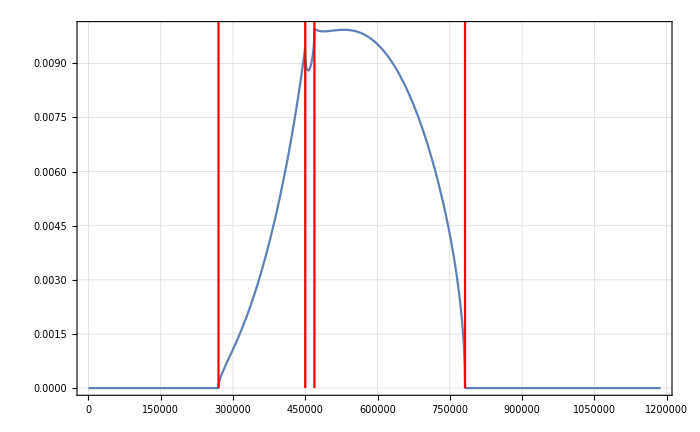

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0,0,xD,{0,0.,p,Pi/4},{Pi,0.2,1,1,1,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->30],
ParametricPlot[{{#,p}&/@test[[2;;-1]]},{p,0,pmax},PlotStyle->Red]
]
```

### DY off, DxRx on

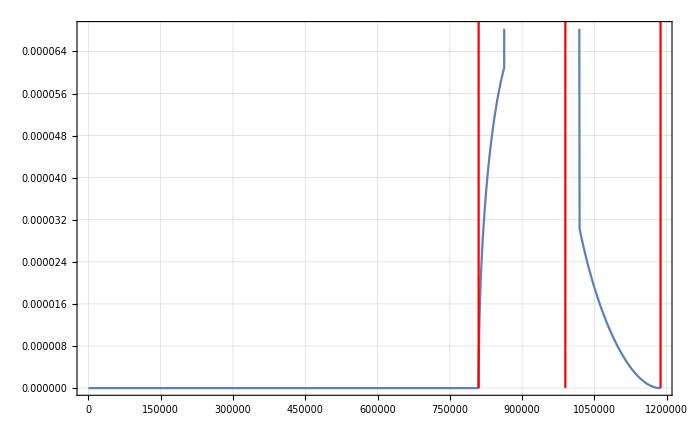

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0,0,xD,{0,0.,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->20],
ParametricPlot[{{#,p}&/@test[[2;;-1]]},{p,0,pmax},PlotStyle->Red]
]
```

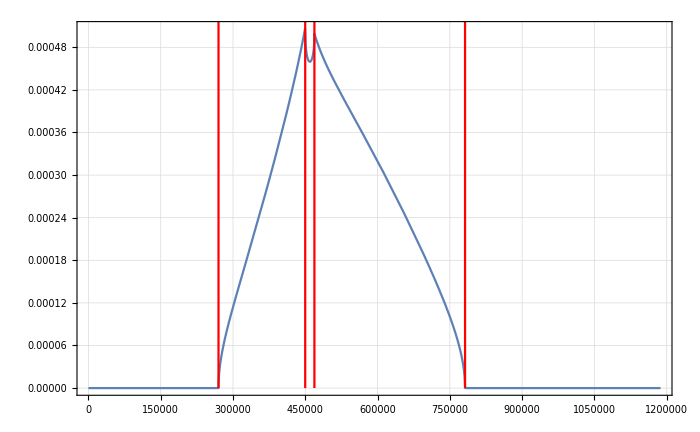

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0,0,xD,{0,0.,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->30],
ParametricPlot[{{#,p}&/@test[[2;;-1]]},{p,0,pmax},PlotStyle->Red]
]
```

```mathematica
xtest=0.03;ytest=-0.0;
```

```mathematica
pminApertShift[0.,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{91339.1}

```mathematica
pminApertShift[-Pi,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{160490.}

```mathematica
pmaxApertShift[0.,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{-91339.1}

```mathematica
pmaxApertShift[-Pi,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{-160490.}

```mathematica
pminApertCasesShift[0.,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{91339.1}

```mathematica
pminApertCasesShift[-Pi,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{160490.}

```mathematica
pmaxApertCasesShift[0.,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{0.}

```mathematica
pmaxApertCasesShift[-Pi,ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{0.}

```mathematica
testplimits=pXDomainShift[ytest,xtest,Pi/4,Pi,0.2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{p,0.,91339.1,160490.}

```mathematica
testplimits2=pXDomainShift[ytest,xtest,Pi/4,Pi,2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{p,0.,913391.,1.18728×10^6}

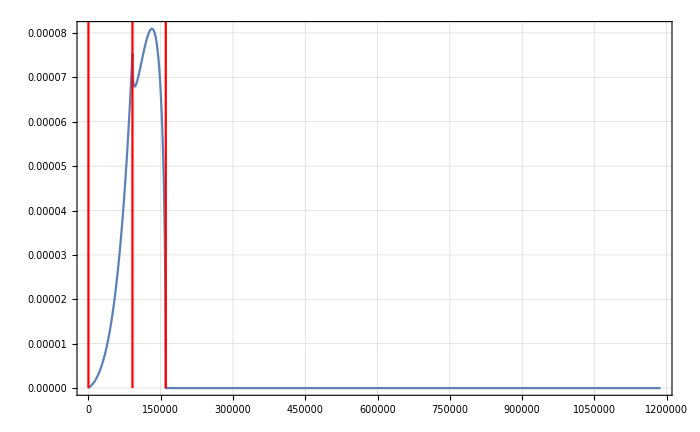

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0,ytest,xtest,{0,0.,p,Pi/4},{Pi,0.2,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->120],
ParametricPlot[{{#,p}&/@testplimits[[2;;-1]]},{p,0,pmax},PlotStyle->Red]
]
```

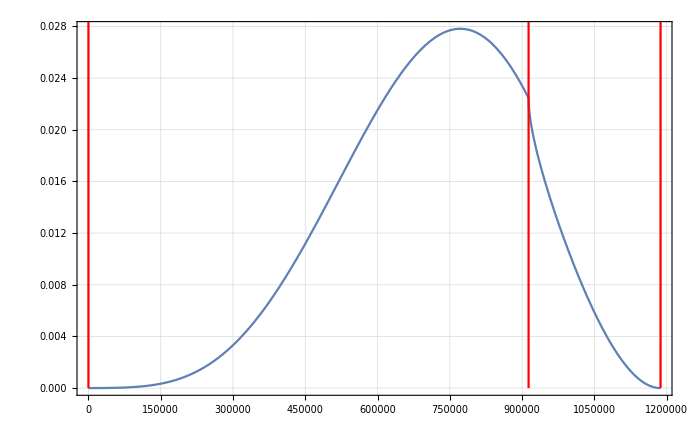

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0,ytest,xtest,{0,0.,p,Pi/4},{Pi,2,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->120],
ParametricPlot[{{#,p}&/@testplimits2[[2;;-1]]},{p,0,pmax},PlotStyle->Red]
]
```

```mathematica
IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

```mathematica
Step1IntShift[0.,ytest,xtest,{0.,Pi/4},{Pi,0.2,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,3,0,2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {159817.,2.16219}. NIntegrate obtained 43.1507 and 0.00670075 for the integral and error estimates.

43.1507

```mathematica
Step1IntShift[0.,ytest,xtest,{0.,Pi/4},{Pi,2,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,3,0,2]
```

86657.3

```mathematica
Step2IntShift[0.,xtest,ytest,{Pi,0.2,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,3,0,2,IntMethod,4,3,0,2]
```

48.1481

### took 99s

```mathematica
Step2IntShift[0.,xtest,ytest,{Pi,2,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,3,0,2,IntMethod,4,3,0,2]
```

196951.

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.2,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,1},{IntMethod,4,3,0,1},{IntMethod,3,3,0,0}]
```

0.34594

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.2,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]
```

$Aborted

```mathematica
BinIntShift[0,{{-0.039999999999999994,-0.03499999999999999},{0.04499999999999993,0.05499999999999994}},{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]
```

0.000229219

```mathematica
BinIntShift[0,{{-0.039999999999999994,-0.03499999999999999},{0.04499999999999993,0.05499999999999994}},{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]
```

0.000228911

```mathematica
{{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}}
```

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.2+0.2*5*10^-5,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,1},{IntMethod,4,3,0,1},{IntMethod,3,3,0,0}]
```

0.345771

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.2+0.2*5*10^-5,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]
```

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.25,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,1},{IntMethod,4,3,0,1},{IntMethod,3,3,0,0}]
```

0.0102076

```mathematica
BinIntShift[0,{-0.04+{-0.005,0.005},0.+{-0.005,0.005}},{Pi,0.3,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,1},{IntMethod,4,3,0,1},{IntMethod,3,3,0,0}]
```

5.04264×10^-7

```mathematica
?Step1IntShift
```

```mathematica
Step1IntShift[0,0.005,-0.035,{0.,0.5},{π,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{"GlobalAdaptive",Method->"MultidimensionalRule"},4,3,0,1]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {p}.

NIntegrate[ManualphiAIntegrandAllLimitsShift[0,0.005,-0.035,{phiDV,0.,p,0.5},{π,2.,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p},{phiDV,-π,π},Method→{GlobalAdaptive,Method→MultidimensionalRule},PrecisionGoal→4,AccuracyGoal→3,MinRecursion→0,MaxRecursion→1]

```mathematica
pXDomainShift[0.005,-0.035,0.5,Pi,2,1,1,1,0.,1,1,0.03,0.01,{0.,0.006,0.,0.015}]
```

{p}

```mathematica
Plot3D[ManualphiAIntegrandAllLimitsShift[0.0015,0.014998,-0.03,{phiDV,Pi,p,0.775079},{3.14351,0.21969,0.994672,0.994885,0.945813,0.965547,0.974009},{0.,0.00718805,0.00677285,0.,0.015928},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{phiDV,-Pi,Pi},{p,0,pmax}]
```

-Graphics3D-

# Timing for precision settings

```mathematica
xtest=-0.04;ytest=0;
```

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{2514.68,0.0611984}

### increase Maxrec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,2}]]
```

{1646.84,0.0611984}

### increase Prec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

{1624.01,0.0611984}

### increase Prec1

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{1602.4,0.0611985}

### both 1 and 3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

{1582.04,0.0611985}

### and maxrec3 more if needed

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]]
```

{1570.99,0.0611985}

```mathematica
0.0000001/0.0611985
```

1.63403×10^-6

## again with dB

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{2476.46,0.0611554}

```mathematica
0.06119843432676003
```

### increase Maxrec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,2}]]
```

{1657.1,0.0611554}

```mathematica
0.06119843432676003
```

### increase Prec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

{1629.12,0.0611554}

### increase Prec1

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{1605.,0.0611554}

```mathematica
0.06119845616399529
```

### both 1 and 3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

{1590.56,0.0611554}

```mathematica
0.06119845616399529
```

### and maxrec3 more if needed

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*5*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]]
```

{1583.35,0.0611554}

```mathematica
0.06119845616399529
```

```mathematica
0.0000001/0.0611985
```

1.63403×10^-6

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[4]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
1580/3600.
```

0.438889

```mathematica
test=ParallelTable[
{x,
BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]
},{x,{4,8,12,16}}]
```

{{4,0.061164},{8,0.0611296},{12,0.0610953},{16,0.0610609}}

```mathematica
ListPlot[test]
```

## now, different point to make sure

```mathematica
xtest=-0.01;ytest=0.02;
```

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{16675.9,2.94896}

### increase Maxrec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,2}]]
```

{13953.,2.94896}

### increase Prec3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.00827938,0.0221103}. NIntegrate obtained 2.94896 and 0.00216093 for the integral and error estimates.

{13755.5,2.94896}

### increase Prec1

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,1}]]
```

{16632.,2.94896}

### both 1 and 3

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,1}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.00827938,0.0221103}. NIntegrate obtained 2.94896 and 0.00216847 for the integral and error estimates.

{16495.1,2.94896}

### and maxrec3 more if needed

```mathematica
AbsoluteTiming[BinIntShift[0,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},
{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,3,0,2},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]]
```

$Aborted

```mathematica
0.0000001/0.0611985
```

1.63403×10^-6

# Investigate required accuracy settings

```mathematica
IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}={{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}};

ApertXOff=0.03;
ApertYOff=0.;

(*CenterfitG1=0.96907;
CenterfitG2=0.973888;*)
BlinefitG1=0.965547;
BlinefitG2=0.974009;

rF=BF/BDV;
rA=BA/BDV;
rRxB=BRxB/BDV;
rDet=BDet/BRxB;

(*AlphaFromBlines=178.20869281586448/180*Pi;*)

AlphaFromBlinesCorr=180.11/180.*Pi;

(*BfromCenter=0.221032;*)

BfromCentralBline=0.219679000;

XAShift=0.0;YAShift=0.007188045691239971;YRxBShift=0.00677284727516161;YDetShift=0.015928000000000164;
XRxBShift=0.;XDetShift=0.;

R=0.999002;

DetHisto={{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778*10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};

(*XYBinBoundariesOriginal=Flatten[Table[{{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},{-DetHisto[[2,yi+1]]-R,-DetHisto[[2,yi]]-R}},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];*)

XYBinBoundariesYHalf=Flatten[Table[{{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

## x=-0.03,y=0.

```mathematica
xtest=-0.03;ytest=0;thtest=Pi/4;phiDettest=0.;
```

## 2D

```mathematica
{{AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{AlphaFromBlinesCorr,BfromCentralBline,rRxB,rA,rDet,BlinefitG1,BlinefitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},IntMethod,6,6,0,12]]}}
```

{{{0.701843,133.007}}}

```mathematica
AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{AlphaFromBlinesCorr,BfromCentralBline+BfromCentralBline*10^-4,rRxB,rA,rDet,BlinefitG1,BlinefitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},IntMethod,6,6,0,12]]
```

{0.634575,132.48}

```mathematica
{0., 0., Pi/4, Pi, BfromCentralBline+BfromCentralBline, rRxB, rA, rDet, 0., BlinefitG1, BlinefitG2,ApertXOff, ApertX, {XAShift, YRxBShift, XDetShift, YDetShift}}
```

{0.,0.,π/4,π,0.439358,0.994672,0.994885,0.945813,0.,0.965547,0.974009,0.03,0.01,{0.,0.00677285,0.,0.015928}}

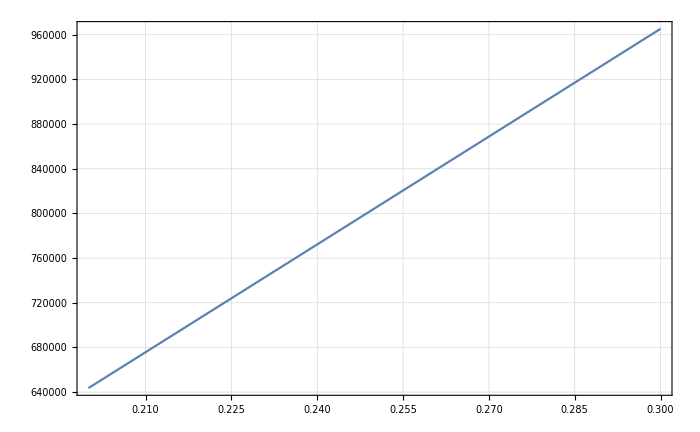

```mathematica
Plot[pminApertShift[0,0., 0., Pi/4, Pi, B, rRxB, rA, rDet, 0., BlinefitG1, BlinefitG2,ApertXOff, ApertX, {XAShift, YRxBShift, XDetShift, YDetShift}],{B,0.2,0.3}]
```

```mathematica
NSolve[0.03+0.01/2==xAShift[0.,ytest,xtest,plocal,Pi/4,Pi,B,rRxB,rA,rDet,0.,BlinefitG1, BlinefitG2,{XAShift,YRxBShift,XDetShift,YDetShift}],plocal,Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{plocal→3.21783×10^6 B}}

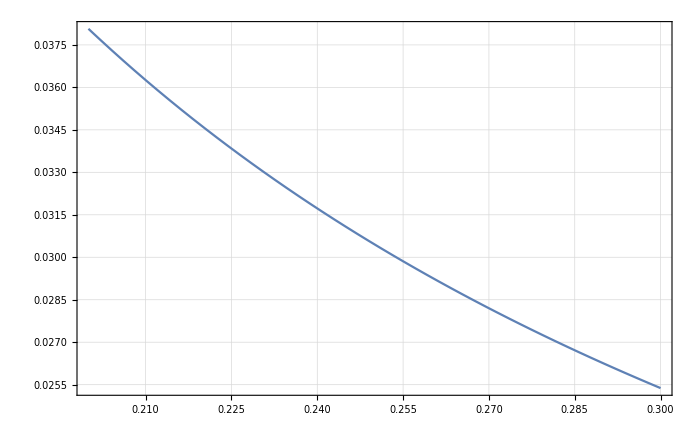

```mathematica
Plot[xAShift[0.,ytest,xtest,700000,Pi/4,Pi,B,rRxB,rA,rDet,0.,BlinefitG1, BlinefitG2,{XAShift,YRxBShift,XDetShift,YDetShift}],{B,0.2,0.3}]
```

```mathematica
pminApertShift[0,0., 0., Pi/4, Pi, BfromCentralBline, rRxB, rA, rDet, 0., BlinefitG1, BlinefitG2,ApertXOff, ApertX, {XAShift, YRxBShift, XDetShift, YDetShift}]
```

{706889.}

```mathematica
pminApertShift[0,0., 0., Pi/4, Pi, BfromCentralBline+BfromCentralBline, rRxB, rA, rDet, 0., BlinefitG1, BlinefitG2,ApertXOff, ApertX, {XAShift, YRxBShift, XDetShift, YDetShift}]
```

{1.41378×10^6}

```mathematica
pLimitsApertXListShift[0., 0., Pi/4, Pi, BfromCentralBline+BfromCentralBline, rRxB, rA, rDet, 0., BlinefitG1, BlinefitG2,ApertXOff, ApertX, {XAShift, YRxBShift, XDetShift, YDetShift}]
```

{505019.,707027.,891641.,1.18728×10^6}

```mathematica
10^-5*132.743
```

0.00132743

```mathematica
{{AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3]]}}
```

{{{0.228548,1.54276}}}

```mathematica
AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,2,0,3]]
```

{0.101911,1.54276}

```mathematica
AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,2,0,2]]
```

{0.103867,1.54276}

```mathematica
0.435/33312.8//ScientificForm
```

1.3058×10^-5

### check x and y regions

```mathematica
Plot3D[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3],{xtest,-0.04,0.03},{ytest,-0.03,0.03},PlotPoints->3]
```

-Graphics3D-

### took 64 s for prec5, acc4 minmax 0,2

### not different for acc3 or acc2

### 155s for prec5,acc2,min1,max2

### 110s for prec5,acc2,min0,max3

### check phiDet and theta regions

```mathematica
Plot3D[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,4,0,2],{thtest,0,Pi/4},{phiDettest,-Pi,Pi},PlotPoints->3]
```

-Graphics3D-

### check dependence on parameter

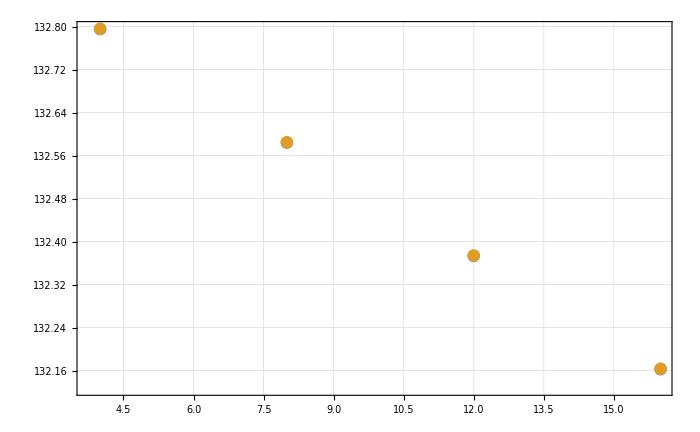

```mathematica
ListPlot[Table[{x,Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{AlphaFromBlinesCorr,BfromCentralBline+BfromCentralBline*x*10^-5,rRxB,rA,rDet,BlinefitG1,BlinefitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},IntMethod,prec,2,0,3]},{prec,4,5},{x,{4,8,12,16}}]]
```

```mathematica
1/33312.//ScientificForm
```

3.00192×10^-5

## 4D

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,2,0,3,IntMethod,4,2,0,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.81011}. NIntegrate obtained 111.521 and 0.159668 for the integral and error estimates.

{174.18,111.521}

```mathematica
0.159/111.52
```

0.00142575

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,2,0,3,IntMethod,4,2,0,3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1856.41,111.524}

```mathematica
7599*10^-4.
```

0.7599

```mathematica
14.12/7599.21
```

0.00185809

```mathematica
ListPlot3D[Flatten[ParallelTable[{xtest,ytest,Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,2]},{xtest,-0.04,0.03,0.02},{ytest,-0.03,0.03,0.02}],1]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,2.68768}. NIntegrate obtained 31777.6 and 867.141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,3.08038}. NIntegrate obtained 2578.39 and 21.0424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,2.68768}. NIntegrate obtained 14773.2 and 227.214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.714671,3.08038}. NIntegrate obtained 594.293 and 0.357422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.81011}. NIntegrate obtained 1475.66 and 0.697835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,0.331487}. NIntegrate obtained 505.029 and 24.2821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.02471}. NIntegrate obtained 35364.8 and 54.8286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.551105,-0.0612125}. NIntegrate obtained 16497.9 and 154.818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.41741}. NIntegrate obtained 611.147 and 0.297704 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in th0 near {th0,phiDet} = {0.186219,2.89674}. NIntegrate obtained 11051.3 and 111.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics3D-

### took 869s

### parameter dependence

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.714671,3.08038}. NIntegrate obtained 7596.69 and 14.1196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.714671,3.08038}. NIntegrate obtained 7594.18 and 14.1149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.714671,3.08038}. NIntegrate obtained 7589.14 and 14.0819 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

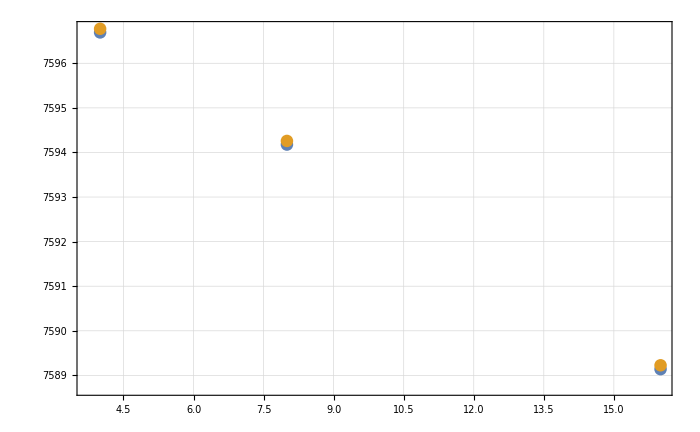

```mathematica
ListPlot[ParallelTable[{x,Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,4,2,0,2,IntMethod,4,3,0,maxrec]},{maxrec,2,3},{x,{4,8,16}}]]
```

### took 3354s

```mathematica
80./70608
```

0.00113302

```mathematica
262/70591.
```

0.00371152

## 6D

### parameter variation

```mathematica
xtest
```

-0.03

```mathematica
ytest
```

0

```mathematica
test=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,2}]]
},{x,{0,8,16}}]
```

{{0,{3228.26,0.384148}},{8,{3280.12,0.384148}},{16,{3380.85,0.384142}}}

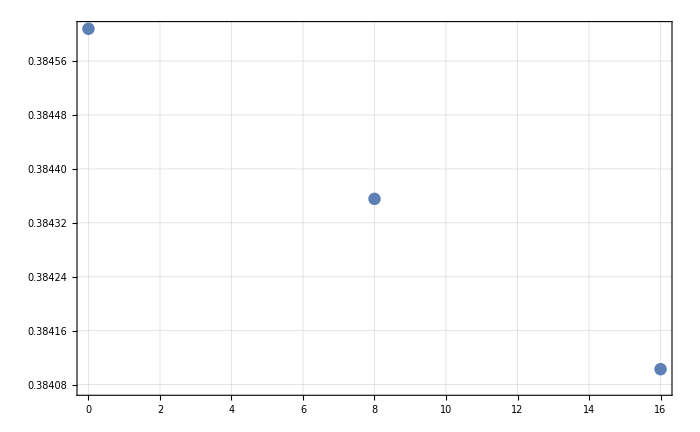

```mathematica
ListPlot[Transpose[{test[[All,1]],test[[All,2,2]]}]]
```

```mathematica
2.5/3844.5
```

0.00065028

```mathematica
3844.5*10^-4
```

0.38445

```mathematica
test=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,2}]]
},{x,{0,8,16}}]
```

{{0,{3329.83,0.384604}},{8,{3300.77,0.384351}},{16,{3293.68,0.384099}}}

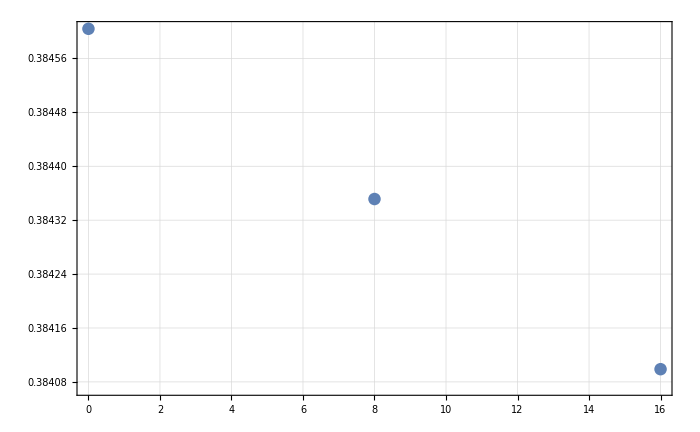

```mathematica
ListPlot[Transpose[{test[[All,1]],test[[All,2,2]]}]]
```

```mathematica
Table[0.21968998395+0.21968998395*x*10^-5,{x,{0,8,16}}]
```

{0.21969,0.219708,0.219725}

```mathematica
Table[0.219679+0.219679*x*10^-5,{x,{0,7.5,15}}]
```

{0.219679,0.219695,0.219712}

### grab parameters again from script

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}={{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}};

ApertXOff=0.03;
ApertYOff=0.;

(*CenterfitG1=0.96907;
CenterfitG2=0.973888;*)
BlinefitG1=0.965547;
BlinefitG2=0.974009;

rF=BF/BDV;
rA=BA/BDV;
rRxB=BRxB/BDV;
rDet=BDet/BRxB;

(*AlphaFromBlines=178.20869281586448/180*Pi;*)

AlphaFromBlinesCorr=180.11/180.*Pi;

(*BfromCenter=0.221032;*)

BfromCentralBline=0.219679000;

XAShift=0.0;YAShift=0.007188045691239971;YRxBShift=0.00677284727516161;YDetShift=0.015928000000000164;
XRxBShift=0.;XDetShift=0.;

R=0.999002;

DetHisto={{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778*10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};

(*XYBinBoundariesOriginal=Flatten[Table[{{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},{-DetHisto[[2,yi+1]]-R,-DetHisto[[2,yi]]-R}},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];*)

XYBinBoundariesYHalf=Flatten[Table[{{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
ParallelTable[
{
x,
AbsoluteTiming[BinIntShift[0.,{-0.03+{-0.0025,0.0025},0.+{-0.005,0.005}},
{AlphaFromBlinesCorr,BfromCentralBline+BfromCentralBline*x*10^-5,rF,rRxB,rA,rDet,BlinefitG1,BlinefitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,2}]]},
{x,{0,8,16}},Method->"FinestGrained"];
```

```mathematica
IntMethod
```

{GlobalAdaptive,Method→MultidimensionalRule}

```mathematica
%
```

{{0,{3373.32,0.384762}},{8,{3382.17,0.384509}},{16,{3369.28,0.384257}}}

```mathematica
{{0,{3373.319675,0.38476235256733515}},{8,{3382.17494,0.3845092673559732}},{16,{3369.280469,0.38425667896151017}}}
```

{{0,{3373.32,0.384762}},{8,{3382.17,0.384509}},{16,{3369.28,0.384257}}}

```mathematica
SetPrecision[0.38476235256733515,20]
```

0.384762352567335153

```mathematica
{{AlphaFromBlinesCorr,BfromCentralBline,rF,rRxB,rA,rDet,BlinefitG1,BlinefitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff}}
```

{{3.14351,0.219679,2.04214,0.994672,0.994885,0.945813,0.965547,0.974009},{0.,0.00718805,0.00677285,0.,0.015928},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}}

### increase aacc3 to see time

```mathematica
test2=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,3,0,2},{IntMethod,4,6,0,2}]]
},{x,{0,8,16}}]
```

$Aborted

```mathematica
ParallelTable[
   AbsoluteTiming[
      BinIntShift[
        b, {-0.03 + {-0.0025, 0.0025}, 0. + {-0.005, 0.005}}, 
        {AlphaFromBlinesCorr, 
    BfromCentralBline + BfromCentralBline*x*10^-5, rF, rRxB, rA, 
    rDet, BlinefitG1, BlinefitG2}, {XAShift, YAShift, YRxBShift, 
    XDetShift, YDetShift}, 
        {0.1, 0.099, 0.9, 0., -0.9, 0.1, 0.099, 0.9, 
    0., -0.9}, {ApertX, ApertY, ApertXOff, ApertYOff},
        {IntMethod, 5, 2, 0, 3}, {IntMethod, 4, 2, 0, 3}, {IntMethod, 
    4, 7, 0, 3}
        ]] , {x, {0, 8, 12, 16}}, 
   Method -> "FinestGrained"]
```

### the one below got no difference on G PC. I manually took the parameters from evaluation

```mathematica
tesing=ParallelTable[
   AbsoluteTiming[
      BinIntShift[
        0., {-0.03 + {-0.0025, 0.0025}, 0. + {-0.005, 0.005}}, 
       {3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,2,0,3},{IntMethod,4,7,0,2}
        ]] , {x, {0, 8, 16}}, 
   Method -> "FinestGrained"]
```

{{21167.,0.384706},{21230.7,0.384453},{20970.2,0.3842}}

### ok cool. we see change. so we need prec=4 at least. and an accuracy, that allows it test another position

```mathematica
tesing2=ParallelTable[
   AbsoluteTiming[
      BinIntShift[
        0., {-0.02 + {-0.0025, 0.0025}, 0.02 + {-0.005, 0.005}}, 
       {3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,2,0,3},{IntMethod,4,7,0,3}
        ]] , {x, {0, 8, 16}}, 
   Method -> "FinestGrained"]
```

{{26003.6,1.50834},{26098.6,1.50786},{26077.4,1.50739}}

## Center x=-0.,y=0.

```mathematica
xtest=-0.0;ytest=0;thtest=Pi/4;phiDettest=0.;
```

## 2D

```mathematica
{{AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3]]}}
```

{{{0.919154,33312.9}}}

```mathematica
10^-5*33312.9
```

0.333129

```mathematica
{{AbsoluteTiming[Step1IntShift[0.,0,0,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3]]}}
```

{{{0.94779,33312.9}}}

```mathematica
0.435/33312.8//ScientificForm
```

1.3058×10^-5

### check x and y regions

```mathematica
Plot3D[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3],{xtest,-0.04,0.03},{ytest,-0.03,0.03},PlotPoints->3]
```

-Graphics3D-

### took 64 s for prec5, acc4 minmax 0,2

### not different for acc3 or acc2

### 155s for prec5,acc2,min1,max2

### 110s for prec5,acc2,min0,max3

### check phiDet and theta regions

```mathematica
Plot3D[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,4,0,2],{thtest,0,Pi/4},{phiDettest,-Pi,Pi},PlotPoints->3]
```

-Graphics3D-

### check dependence on parameter (by accident different xy point!)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {716229.,2.16219}. NIntegrate obtained 33312.4 and 1.09812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {716258.,2.16219}. NIntegrate obtained 33312. and 1.0981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {716286.,2.16219}. NIntegrate obtained 33311.6 and 1.09808 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

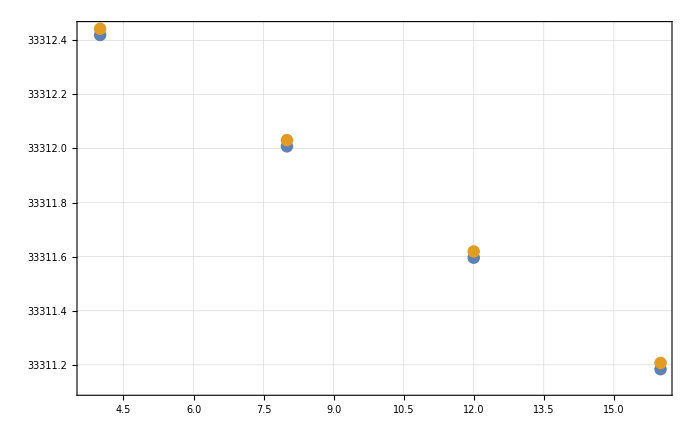

```mathematica
ListPlot[Table[{x,Step1IntShift[0.,0,0,{phiDettest,thtest},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,maxrec]},{maxrec,2,3},{x,{4,8,12,16}}]]
```

```mathematica
1/33312.//ScientificForm
```

3.00192×10^-5

## 4D

```mathematica
xtest
```

-0.01

```mathematica
ytest
```

0.03

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.357336,3.08038}. NIntegrate obtained 18188.7 and 216.652 for the integral and error estimates.

{174.608,18188.7}

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,3]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,2.34089}. NIntegrate obtained 70603.1 and 80.2515 for the integral and error estimates.

{691.171,70603.1}

```mathematica
80/70603.
```

0.0011331

```mathematica
70603*10^-4.
```

7.0603

### minrec2=1

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,1,3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.719086,2.34854}. NIntegrate obtained 70621.5 and 19.0267 for the integral and error estimates.

{1696.6,70621.5}

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,4]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in phiDet near {th0,phiDet} = {0.759977,-0.641962}. NIntegrate obtained 18166.9 and 6.37908 for the integral and error estimates.

{6455.08,18166.9}

```mathematica
ListPlot3D[Flatten[ParallelTable[{xtest,ytest,Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,2]},{xtest,-0.04,0.03,0.02},{ytest,-0.03,0.03,0.02}],1]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,2.68768}. NIntegrate obtained 31777.6 and 867.141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,3.08038}. NIntegrate obtained 2578.39 and 21.0424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.654263,2.68768}. NIntegrate obtained 14773.2 and 227.214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.714671,3.08038}. NIntegrate obtained 594.293 and 0.357422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.81011}. NIntegrate obtained 1475.66 and 0.697835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,0.331487}. NIntegrate obtained 505.029 and 24.2821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.02471}. NIntegrate obtained 35364.8 and 54.8286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.551105,-0.0612125}. NIntegrate obtained 16497.9 and 154.818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-2.41741}. NIntegrate obtained 611.147 and 0.297704 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in th0 near {th0,phiDet} = {0.186219,2.89674}. NIntegrate obtained 11051.3 and 111.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics3D-

### took 869s

### parameter dependence (by accident different xy point!)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,0.331487}. NIntegrate obtained 70591.1 and 262.856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,2.34089}. NIntegrate obtained 70608.1 and 80.2573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,0.331487}. NIntegrate obtained 70596.1 and 262.857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.744875,0.331487}. NIntegrate obtained 70606.2 and 262.841 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,2.34089}. NIntegrate obtained 70613.1 and 80.2623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,2.34089}. NIntegrate obtained 70623.2 and 80.2723 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

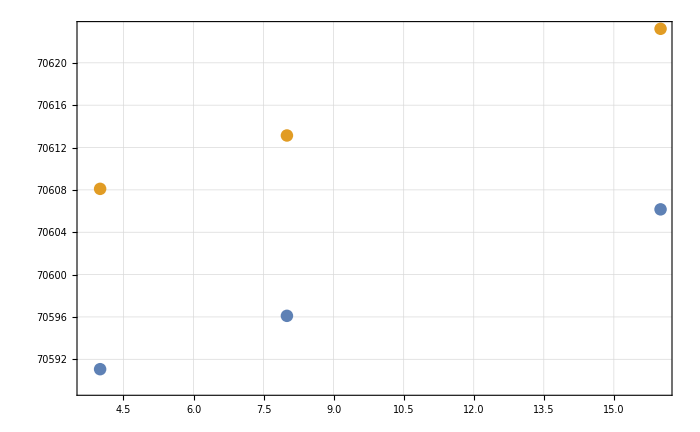

```mathematica
ListPlot[ParallelTable[{x,Step2IntShift[0.,0.,0.,{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,maxrec]},{maxrec,2,3},{x,{4,8,16}}]]
```

```mathematica
80./70608
```

0.00113302

```mathematica
262/70591.
```

0.00371152

## 6D

```mathematica
?BinIntShift
```

### parameter variation

```mathematica
test=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]]
},{x,{0,8,16}}]
```

{{0,{5311.23,0.384608}},{8,{5307.74,0.384356}},{16,{5252.41,0.384103}}}

```mathematica
ListPlot[Transpose[{test[[All,1]],test[[All,2,2]]}]]
```

-Graphics-

```mathematica
2.5/3844.5
```

0.00065028

```mathematica
3844.5*10^-4
```

0.38445

### increase aacc3 to see time

```mathematica
test2=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,3,0,2},{IntMethod,4,6,0,2}]]
},{x,{0,8,16}}]
```

$Aborted

## yoff x=-0.01,y=0.03

```mathematica
xtest=-0.01;ytest=0.03;thtest=Pi/4;phiDettest=0.;
```

## 2D

```mathematica
{{AbsoluteTiming[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3]]}}
```

{{{1.00599,7374.56}}}

```mathematica
10^-5*7374.56
```

0.0737456

### check phiDet and theta regions

```mathematica
Plot3D[Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3],{thtest,0,Pi/4},{phiDettest,-Pi,Pi},PlotPoints->3]
```

-Graphics3D-

```mathematica
20000*10^-4
```

2

### check dependence on parameter (by accident different xy point!)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {893814.,2.16219}. NIntegrate obtained 7374.51 and 2.45329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {893885.,2.16219}. NIntegrate obtained 7372.83 and 2.45346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in p near {p,phiDV} = {893957.,2.16219}. NIntegrate obtained 7371.15 and 2.45363 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

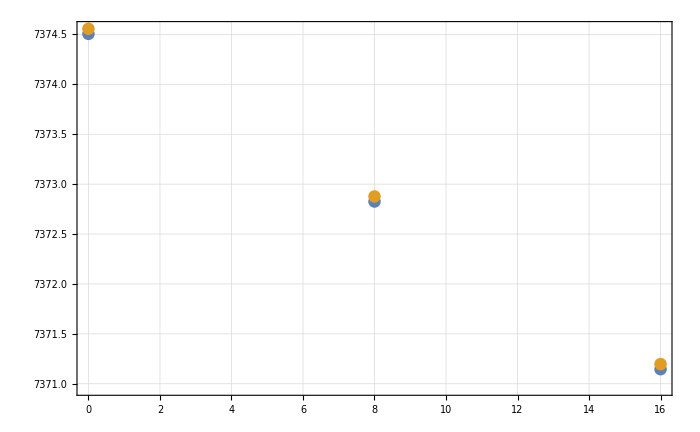

```mathematica
ListPlot[ParallelTable[{x,Step1IntShift[0.,ytest,xtest,{phiDettest,thtest},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,maxrec]},{maxrec,2,3},{x,{0,8,16}}]]
```

```mathematica
2.45/7374.5//ScientificForm
```

3.32226×10^-4

## 4D

```mathematica
AbsoluteTiming[Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,3]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-0.604352}. NIntegrate obtained 18162.8 and 31.9185 for the integral and error estimates.

{1243.52,18162.8}

```mathematica
31.9/18162.8
```

0.0011331

```mathematica
18162.8*10^-4.
```

7.0603

### parameter dependence

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.357336,3.08038}. NIntegrate obtained 18188.7 and 216.652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.357336,3.08038}. NIntegrate obtained 18187.9 and 216.717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in phiDet near {th0,phiDet} = {0.357336,3.08038}. NIntegrate obtained 18187. and 216.802 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-0.604352}. NIntegrate obtained 18162.8 and 31.9185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-0.604352}. NIntegrate obtained 18161.9 and 31.9764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 6 recursive bisections in phiDet near {th0,phiDet} = {0.744875,-0.604352}. NIntegrate obtained 18161.1 and 32.042 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

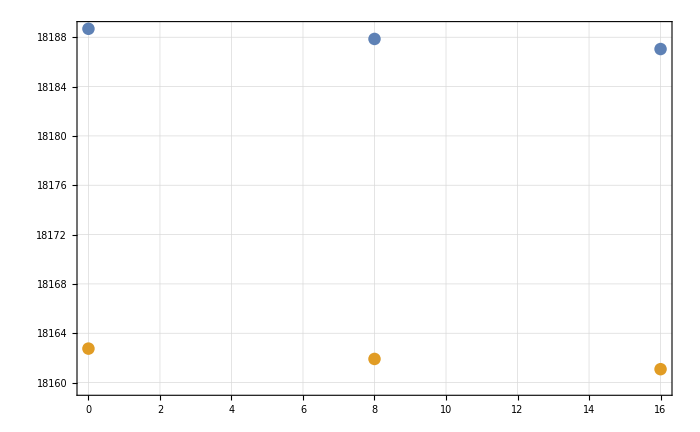

```mathematica
ListPlot[ParallelTable[{x,Step2IntShift[0.,xtest,ytest,{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},IntMethod,5,2,0,3,IntMethod,4,3,0,maxrec]},{maxrec,2,3},{x,{0,8,16}}]]
```

```mathematica
216.65/18188.685
```

0.0119113

```mathematica
31.9/18161.9
```

0.00175642

## 6D

```mathematica
?BinIntShift
```

### parameter variation

```mathematica
test=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2}]]
},{x,{0,8,16}}]
```

{{0,{5311.23,0.384608}},{8,{5307.74,0.384356}},{16,{5252.41,0.384103}}}

```mathematica
ListPlot[Transpose[{test[[All,1]],test[[All,2,2]]}]]
```

-Graphics-

```mathematica
2.5/3844.5
```

0.00065028

```mathematica
3844.5*10^-4
```

0.38445

### increase aacc3 to see time

```mathematica
test2=ParallelTable[{x,AbsoluteTiming[BinIntShift[0.,{xtest+{-0.0025,0.0025},ytest+{-0.005,0.005}},{3.1435125157669868,0.21968998395+0.21968998395*x*10^-5,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{IntMethod,4,3,0,2},{IntMethod,4,6,0,2}]]
},{x,{0,8,16}}]
```

$Aborted

# Lets “quickly” check MC integration for the outer 4 dimensions

```mathematica
ClearAll[Outer4DMCTest]
```

```mathematica
Outer4DMCTest[b_,OneBinList_,{alpha_,BRxB_,rF_,rRxB_,rA_,rD_,G1_,G2_},{XAShift_,YAShift_,YRxBShift_,XDetShift_,YDetShift_},{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_},{method1_,PrecGoal1_,AccGoal1_,MinRec1_,MaxRec1_},{PrecGoal2_,AccGoal2_,MinRec2_,MaxRec2_,MaxP_}]:=
NIntegrate[
Step1IntShift[
b,yD,xD,{phiDet,th0},{alpha,BRxB,rRxB,rA,rD,G1,G2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},
method1,PrecGoal1,AccGoal1,MinRec1,MaxRec1
],
{yD,OneBinList[[2,1]],OneBinList[[2,2]]},
{xD,OneBinList[[1,1]],OneBinList[[1,2]]},
{th0,0.,thetamax[rF]},
{phiDet,-Pi,Pi},
Method->"AdaptiveMonteCarlo",MaxPoints->MaxP,
PrecisionGoal->PrecGoal2,AccuracyGoal->AccGoal2,MinRecursion->MinRec2,MaxRecursion->MaxRec2
]
```

### check timing (same point above took 5300s)

```mathematica
Outer4DMCTest[0.,{-0.03+{-0.0025,0.0025},0.+{-0.005,0.005}},{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{3,2,0,1,10^4}]
```

0.38803

```mathematica
0.388*10^-3
```

0.000388

### took 1190s

```mathematica
AbsoluteTiming[Outer4DMCTest[0.,{-0.03+{-0.0025,0.0025},0.+{-0.005,0.005}},{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{3,4,0,1,10^5}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 5 recursive bisections in yD near {yD,xD,th0,phiDet} = {0.617555,0.698562,0.936534,0.619142}. NIntegrate obtained 0.380615 and 0.00413846 for the integral and error estimates.

{6753.53,0.380615}

```mathematica
(10^5)^(1/4.)
```

17.7828

```mathematica
12^4
```

20736

```mathematica
0.0041/0.3806
```

0.0107725

```mathematica
AbsoluteTiming[Outer4DMCTest[0.,{-0.03+{-0.0025,0.0025},0.+{-0.005,0.005}},{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{3,4,0,2,2*10^4}]]
```

NIntegrate::maxp: The integral failed to converge after 20100 integrand evaluations. NIntegrate obtained 0.386307 and 0.00139072 for the integral and error estimates.

{11360.6,0.386307}

```mathematica
0.00139/0.386
```

0.00360104

```mathematica
AbsoluteTiming[Outer4DMCTest[0.,{-0.03+{-0.0025,0.0025},0.+{-0.005,0.005}},{3.1435125157669868,0.21968998395,2.0421414311517934,0.9946717730727618,0.9948845399933905,0.9458133459553435,0.965547,0.974009},{0.,0.007188045691239971,0.00677284727516161,0.,0.015928000000000164},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.},{IntMethod,5,2,0,3},{3,4,1,3,2*10^4}]]
```

### thats the conventional result

```mathematica
{5311.228097,0.3846078570255975}
```